```mathematica
Needs["Niceplots`"]
```

# Jaynes-Cummings ladder

```mathematica
M =( {{wc*N1, g(√N1)/2}, {g(√N1)/2, wc*(N1) + dac}})
```

{{N1 wc,(g √N1)/2},{(g √N1)/2,dac+N1 wc}}

```mathematica
FullSimplify[Eigenvalues[M]]
```

{1/2 (dac+ⅈ f-√((dac-ⅈ f)^2+g^2 N1)+2 N1 wc),1/2 (dac+ⅈ f+√((dac-ⅈ f)^2+g^2 N1)+2 N1 wc)}

```mathematica
Normal[FullSimplify[Eigenvectors[M]]]
```

{{-(dac+√(dac^2+g^2 N1))/(g √N1),1},{(-dac+√(dac^2+g^2 N1))/(g √N1),1}}

## Add nonHermiticity

```mathematica
M =( {{wc*N1 + ⅈ, g(√N1)/2}, {g(√N1)/2, wc*(N1) + dac}})
```

{{ⅈ+N1 wc,(g √N1)/2},{(g √N1)/2,dac+N1 wc}}

```mathematica
FullSimplify[Eigenvalues[M]]
```

{1/2 (ⅈ+dac-√((-ⅈ+dac)^2+g^2 N1)+2 N1 wc),1/2 (ⅈ+dac+√((-ⅈ+dac)^2+g^2 N1)+2 N1 wc)}

```mathematica
Normal[FullSimplify[Eigenvectors[M]]]
```

{{-(-ⅈ+dac+√((-ⅈ+dac)^2+g^2 N1))/(g √N1),1},{(ⅈ-dac+√((-ⅈ+dac)^2+g^2 N1))/(g √N1),1}}

# non-Hermitian Perturbation for JCH 2nd excitation manifold

```mathematica
g0 = ψ0;
```

```mathematica
g1= {0, 1, 0,0,0};
g2 = {0, 0, 0, 1, 0};
e1 = {0, 0, 0, 0, 1};
e0 = {0,0 , 1, 0, 0};
```

```mathematica
V1.g0
```

{0,0,0,0,0}

```mathematica
V1.g1
```

{1,0,0,0,0}

```mathematica
V1.g2
```

{0,√2,0,0,0}

```mathematica
V1.e0
```

{0,0,0,0,1}

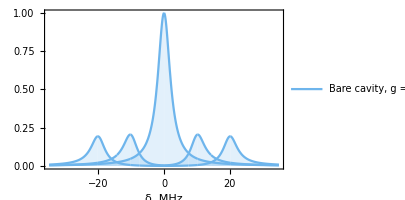

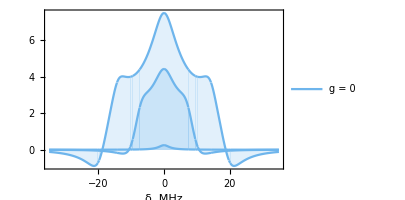

```mathematica
Clear[H0, g, δlc, κ, Γ, V, H0s, δac, ψ1,ψ2,ψt ]
H0 =( {{δlc, 0, 0, 0, 0}, {0, ⅈ κ/2, g/2, 0, 0}, {0, g/2, δac +  ⅈ Γ/2, 0, 0}, {0, 0, 0, -δlc + ⅈ κ, g(√2)/2}, {0, 0, 0, g(√2)/2, - δlc + δac + ⅈ κ/2+ ⅈ Γ/2}});
V = ({{0, 1, 0, 0, 0}, {1, 0, 0, √2, 0}, {0, 0, 0, 0, 1}, {0, √2, 0, 0, 0}, {0, 0, 1, 0, 0}});
V1 = ({{0, 1, 0, 0, 0}, {0, 0, 0, √2, 0}, {0, 0, 0, 0, 1}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
H0s =({{ⅈ κ/2, g/2, 0, 0}, {g/2, δac +  ⅈ Γ/2, 0, 0}, {0, 0, -δlc + ⅈ κ, g(√2)/2}, {0, 0, g(√2)/2, - δlc + δac + ⅈ κ/2+ ⅈ Γ/2}});
ψ0c ={1, 0, 0,0,0};
ψ0 = Eigenvectors[H0][[1]];
E0 = Eigenvalues[H0][[1]];
Q = IdentityMatrix[5] - Outer[Times, ψ0 , ψ0c ];
InverseH0 = FullSimplify[Inverse[H0s - E0*IdentityMatrix[4]]];
v = {0, 0,0 , 0};
v2 = {0, 0, 0, 0, 0};
m11 = Insert[InverseH0, v, 1];
InverseH0Final =Insert[m11ᵀ, v2, 1];
E1 = ψ0c.V.ψ0;
(*E2 = FullSimplify[ψ0c.V.Q .InverseH0Final.Q.V. ψ0];
ψ1 = InverseH0Final.Q.V.ψ0;
ψ2 =InverseH0Final.Q.V.InverseH0Final.Q.V.ψ0;*)
E2 = FullSimplify[ψ0c.V .InverseH0Final.V. ψ0];
ψ1 =InverseH0Final.V.ψ0;
ψ2 =InverseH0Final.V.InverseH0Final.V.ψ0;
ψt = Normalize[FullSimplify[ψ0 + Ω* ψ1 + Ω^2 ψ2]];
phot1 = {0,1, 0, 0, 0};
phot2 = {0, 0, 0, 1, 0};
(*Trans = Conjugate[ψ0 +ψ1].Transpose[V1].V1. (ψ0 +ψ1);
g2 = Conjugate[ψ0 +ψ1+ψ2].Transpose[V1].Transpose[V1].V1.V1.(ψ0 +ψ1+ψ2);*)
Trans = phot1. ψt;
g2 = phot2.ψt;
Clear[params, NormTrans]
params={{Γ->6, κ->4, g-> 0, Ω-> 1, δac->0}, {Γ->6, κ->4, g->  10*2, Ω-> 1, δac->0}, {Γ->6, κ->4, g->  20*2, Ω-> 1, δac->0}};
NormTrans =((Abs[Trans])^2/.params[[1]])/.δlc->0;
TransFinal =(((Abs[Trans]))^2/.params);
Normg2 =Abs[g2/.params]/TransFinal /.δlc-> -50;
g2Final =(Abs[g2/.params])^2/(1/2( TransFinal)^2 );
(*NormTrans =((Abs[Trans])/.params[[1]])/.δlc->0;
TransFinal =(((Abs[Trans]))/.params);
Normg2 =((Abs[g2/.params])/(TransFinal^2 ))/.δlc-> -50;
g2Final =((Abs[g2/.params]) /((1/2 )TransFinal^2 ));*)
transm =Plot[(TransFinal/NormTrans), {δlc, -35, 35}, PlotRange->All,  PlotStyle->colorGradToIndexed["Pastel", 3],Filling->Axis, PlotLegends-> Placed[{"Bare cavity, g = 0", "Vacuum Rabi Splitting, g = 10",  "Vacuum Rabi Splitting, g = 15"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
g2p=Plot[Log[g2Final[[]]],{δlc,-35,35},PlotRange->All,PlotStyle->colorGradToIndexed["Pastel",3],PlotLegends->Placed[{"g = 0","g = 10","g = 15"},Right],AspectRatio->2/3,Filling->0,ImageSize->300,ImagePadding->All,ImageMargins->0,Frame->{{True,True},{True,True}},FrameStyle->{{Black,Automatic},{Black,Automatic}},FrameLabel->{{None,None},{Style["δ, MHz",FontSize->16,Black],Style["\!\(\*SubscriptBox[\(g\), \(2\)]\)(0)",FontSize->16,Black,Bold]}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[Black],BaseStyle->{FontWeight->Automatic,FontSize->16,Bold}]
```

```mathematica
g2Final[[2]]/.δlc->1
```

(26216189 √(26216189/145))/1902690

```mathematica
FullSimplify[(2 √2 g^2)/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))-(ⅈ √2 (-2 ⅈ Γ-4 δac+4 δlc) (Γ-2 ⅈ δac+4 ⅈ δlc+κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))]
```

(2 √2 (g^2-(Γ-2 ⅈ (δac-δlc)) (Γ-2 ⅈ δac+4 ⅈ δlc+κ)))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))

```mathematica
FullSimplify[(2 g (-2 ⅈ Γ-4 δac+4 δlc))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))+(2 g (4 δlc-2 ⅈ κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))]
```

-(4 ⅈ g (Γ-2 ⅈ δac+4 ⅈ δlc+κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))

```mathematica
(phot1.ψ1)/.params[[2]]
```

(-12 ⅈ+4 δlc)/(400+(6 ⅈ-2 δlc) (-4 ⅈ+2 δlc))

```mathematica
ψ1//MatrixForm
```

(0
-(2 ⅈ (Γ-2 ⅈ δac) Ω)/(g^2+Γ κ-2 ⅈ δac κ)
(2 g Ω)/(g^2+Γ κ-2 ⅈ δac κ)
0
0)

```mathematica
V.V.ψ1//MatrixForm
```

(0
-(6 ⅈ (Γ-2 ⅈ δac) Ω)/(g^2+Γ κ-2 ⅈ δac κ)
0
0
0)

```mathematica
(Conjugate[ψ1].V.V.ψ1)
```

(12 (Γ-2 ⅈ δac) Ω (Conjugate[Γ]+2 ⅈ Conjugate[δac]) Conjugate[Ω])/((g^2+Γ κ-2 ⅈ δac κ) (Conjugate[g]^2+Conjugate[Γ κ-2 ⅈ δac κ]))

```mathematica
ψ2//MatrixForm
```

(0
0
0
-(ⅈ √2 (-2 ⅈ Γ-4 δac+4 δlc) (Γ-2 ⅈ δac+4 ⅈ δlc+κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))
(2 g (-2 ⅈ Γ-4 δac+4 δlc))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ))))

```mathematica
V.ψ2//MatrixForm
```

(0
-(2 ⅈ (-2 ⅈ Γ-4 δac+4 δlc) (Γ-2 ⅈ δac+4 ⅈ δlc+κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))
0
0
0)

```mathematica
ψ0.V.V.ψ2//MatrixForm
```

-(2 ⅈ (-2 ⅈ Γ-4 δac+4 δlc) (Γ-2 ⅈ δac+4 ⅈ δlc+κ))/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ)) (g^2+(2 δlc-ⅈ κ) (ⅈ Γ+2 δac-4 δlc+ⅈ κ)))

```mathematica
ψ1.Transpose[V].V.( ψ1)
```

(3 (-2 ⅈ Γ-4 δac+4 δlc)^2)/((g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ))^2)

```mathematica
ψ0c ={1, 0, 0,0,0};
ψ0 = Eigenvectors[H0][[1]];
E0 = Eigenvalues[H0][[1]];
Q = IdentityMatrix[5] - Outer[Times, ψ0 , ψ0c ];
InverseH0 = Inverse[H0 - E0*IdentityMatrix[5]-b*IdentityMatrix[5]];
```

```mathematica
E1 = ψ0c.V.ψ0;
ψ1 = InverseH0.V.ψ0;
E2 =ψ0c.V.ψ1;
ψ2 =InverseH0.V.ψ1;
ψt = Normalize[FullSimplify[ψ0 + Ω* ψ1 + Ω^2 ψ2]];
phot1 = {0,1, 0, 0, 0};
phot2 = {0, 0, 0, 0, 1};
Trans = phot1.ψ1;
g2 = phot2.ψ2;
```

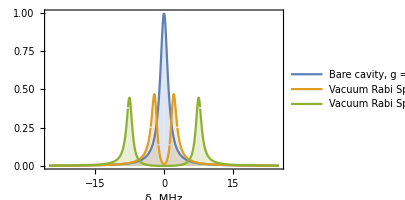

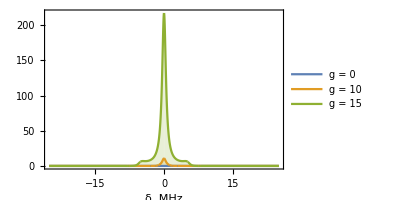

```mathematica
params={{Γ->1, κ->2, g-> 0, Ω-> .01, δac->0, b->.0000000001}, {Γ->1, κ->2, g->  4, Ω-> .01, δac->0,b->.0000000001}, {Γ->1, κ->2, g->  15, Ω-> .01, δac->0,b->.0000000001}};
NormTrans =(((Abs[Trans])^2)/.params[[1]])/.δlc->0;
TransFinal =(((Abs[Trans])^2)/.params)/NormTrans;
Normg2 =((Abs[g2/.params])^2/(TransFinal^2 ))/.δlc-> -50;
g2Final =(1/2(Abs[g2/.params]^2) /(1/2 TransFinal^2 ));
transm =Plot[(TransFinal), {δlc, -25, 25}, PlotRange->All, PlotStyle->colorGradToIndexed["Pastel", 3],Filling->Axis, PlotLegends-> Placed[{"Bare cavity, g = 0", "Vacuum Rabi Splitting, g = 10",  "Vacuum Rabi Splitting, g = 15"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
g2p=Plot[g2Final,{δlc,-25,25},PlotRange->All,PlotStyle->colorGradToIndexed["Pastel",3],PlotLegends->Placed[{"g = 0","g = 10","g = 15"},Right],AspectRatio->2/3,Filling->1,ImageSize->300,ImagePadding->All,ImageMargins->0,Frame->{{True,True},{True,True}},FrameStyle->{{Black,Automatic},{Black,Automatic}},FrameLabel->{{None,None},{Style["δ, MHz",FontSize->16,Black],Style["\!\(\*SubscriptBox[\(g\), \(2\)]\)(0)",FontSize->16,Black,Bold]}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[Black],BaseStyle->{FontWeight->Automatic,FontSize->16,Bold}]
```

# non-Hermitian Perturbation for EIT

1 excitation manifold many atom

```mathematica
Clear[H0, g, δlc, κ, Γ, V, H0s, δac, ΓR]
Nat  = 1;
H0 =( {{δlc, 0, 0, 0}, {0, ⅈ κ/2, √Nat *g/2, 0}, {0, √Nat *g/2, δac +  ⅈ Γ/2, gR/2}, {0, 0, gR/2, ΔblueR + (ⅈ ΓR)/2}});
V = ({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
H0s =({{ⅈ κ/2, √Nat *g/2, 0}, {√Nat *g/2, δac +  ⅈ Γ/2, gR/2}, {0, gR/2, ΔblueR + (ⅈ ΓR)/2}});
Special state for normalizing
ψ0c ={1, 0, 0,0};
ψ0 = Eigenvectors[H0][[1]];
E0 = Eigenvalues[H0][[1]];
Projection operator to project onto space perpendicular to ψ0c
Q = IdentityMatrix[4] - Outer[Times, ψ0 , ψ0c ];
InverseH0 = FullSimplify[Inverse[H0s - E0*IdentityMatrix[3]]];
v = {0, 0,0 };
v2 = {0, 0, 0, 0};
m11 = Insert[InverseH0, v, 1];
InverseH0Final =Insert[m11ᵀ, v2, 1];
E1 = ψ0c.V.ψ0;
E2 = FullSimplify[ψ0c.V.Q .InverseH0Final.Q.V. ψ0];
ψ1 = InverseH0Final.Q.V.ψ0;
ψt = FullSimplify[ψ0 + Ω* ψ1 ];
phot1 = {0,1, 0, 0};
Trans = FullSimplify[phot1.ψ1];
```

for normalizing Special state

{onto operator perpendicular project Projection space to^2,0,0,0}

```mathematica
Trans
```

-(2 (gR^2+(Γ-2 ⅈ (δac-δlc)) (ΓR-2 ⅈ (ΔblueR-δlc))))/(g^2 (-ⅈ ΓR-2 ΔblueR+2 δlc)+(gR^2+(Γ-2 ⅈ δac+2 ⅈ δlc) (ΓR-2 ⅈ ΔblueR+2 ⅈ δlc)) (2 δlc-ⅈ κ))

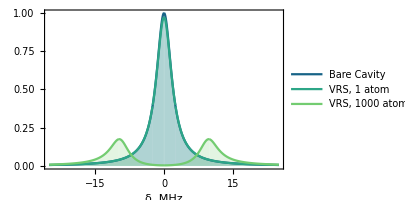

```mathematica
Clear[params, NormTrans]
params={{Γ->6,ΓR->.03, κ->4, g-> 0, gR-> 0, Ω-> .01, δac->0, ΔblueR->0}, {Γ->6,ΓR->.03, κ->4, g->  .6, gR-> 0,Ω-> .01, δac->0, ΔblueR->0},{Γ->6,ΓR->.03, κ->4, g->  0.6*√1000, gR-> 0,Ω-> .01, δac->0, ΔblueR->0}};
NormTrans =(Abs[Trans/.params[[1]]]^2)/.δlc->0;
TransFinal =(((Abs[Trans])^2)/.params)/NormTrans;
Normg2 =((Abs[g2/.params])^2/ TransFinal^2)/.δlc-> 100;
g2Final =((Abs[g2/.params])^2 / TransFinal^2)/Normg2;
manyatomVRS =Plot[{TransFinal[[1]],TransFinal[[2]], TransFinal[[3]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->colorGradToIndexed["BlueGreenYellow", 4],Filling->Axis, PlotLegends-> Placed[{ "Bare Cavity", "VRS, 1 atom",  "VRS, 1000 atoms"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
```

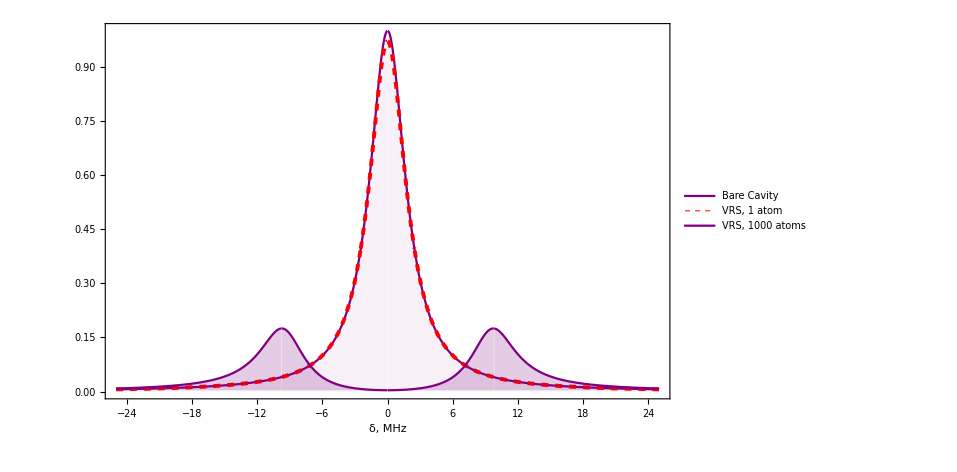

```mathematica
manyatomVRS =Show[{Plot[{TransFinal[[1]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->Purple,Filling->Axis,FillingStyle->{LightPurple,Opacity[0.06]},PlotLegends-> Placed[{ "Bare Cavity"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}],Plot[{TransFinal[[2]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->{Red, Dashed, Thickness[0.004]},Filling->None, FillingStyle->None,PlotLegends-> Placed[{ "VRS, 1 atom"}, Right],AspectRatio->1, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}],Plot[{TransFinal[[3]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->Purple,Filling->Axis, FillingStyle->Opacity[0.2],PlotLegends-> Placed[{  "VRS, 1000 atoms"}, Right],AspectRatio->1, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]}]
```

```mathematica
Export["manyatomVRS.pdf", manyatomVRS]
```

manyatomVRS.pdf

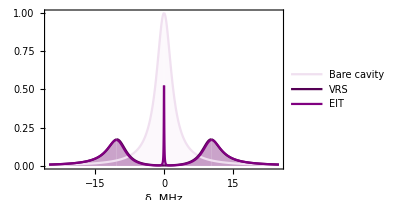

```mathematica
Clear[params, NormTrans]
params={{Γ->6,ΓR->.03, κ->4, g-> 0, gR-> 0, Ω-> .01, δac->0, ΔblueR->0},{Γ->6,ΓR->.03, κ->4, g->  20, gR-> 0,Ω-> .01, δac->0, ΔblueR->0}, {Γ->6,ΓR->.03, κ->4, g->  20, gR-> 3,Ω-> .01, δac->0, ΔblueR->0}};
NormTrans =(Abs[Trans/.params[[1]]]^2)/.δlc->0;
TransFinal =(((Abs[Trans])^2)/.params)/NormTrans;
Normg2 =((Abs[g2/.params])^2/ TransFinal^2)/.δlc-> 100;
g2Final =((Abs[g2/.params])^2 / TransFinal^2)/Normg2;
manyatomEIT =Plot[TransFinal, {δlc, -25, 25}, PlotRange->All,Filling->Axis,PlotStyle->{LightPurple, Darker[Purple], Purple}, PlotLegends-> Placed[{"Bare cavity", "VRS",  "EIT"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
```

```mathematica
Export["manyatomEIT.pdf", manyatomEIT]
```

manyatomEIT.pdf

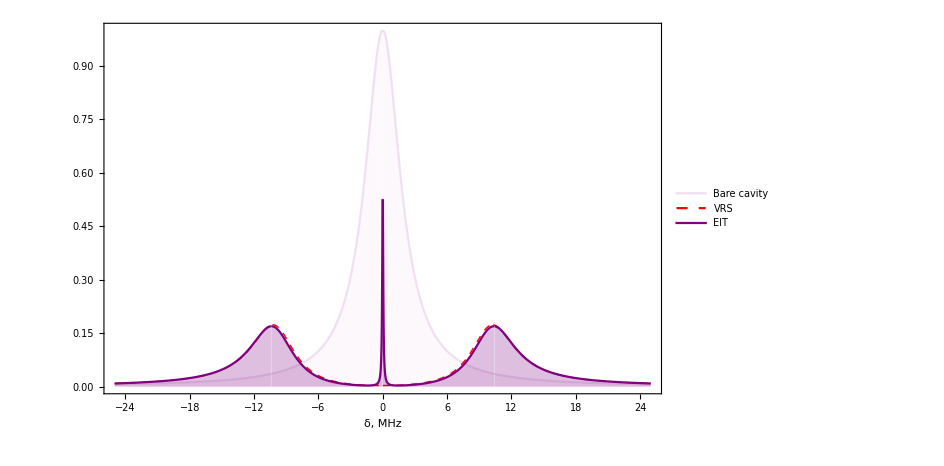

```mathematica
manyatomEIT =Show[{Plot[{TransFinal[[1]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->LightPurple,Filling->Axis,AspectRatio->2/3, ImageSize->300,PlotLegends-> Placed[{"Bare cavity"}, Right],ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}],Plot[{TransFinal[[2]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->{Red, Thick, Dashed},Filling->None, FillingStyle->LightPurple,AspectRatio->2/3,PlotLegends-> Placed[{ "VRS"}, Right], ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}],Plot[{TransFinal[[3]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->Purple,Filling->Axis, FillingStyle->Opacity[0.25],AspectRatio->2/3, ImageSize->300,PlotLegends-> Placed[{"EIT"}, Right],ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]}]
```

# non-Hermitian Perturbation for mmwaves 1 excitation

1 excitation manifold many atom

```mathematica
Clear[H0, g, δlc, κ, Γ, V, H0s, δac, ΓR, gmm]
Nat  = 1;
H0 =({{δlc, 0, 0, 0, 0}, {0, ⅈ κ/2, √Nat *g/2, 0, 0}, {0, √Nat *g/2, δac +  ⅈ Γ/2, gR/2, 0}, {0, 0, gR/2, ΔblueR + (ⅈ ΓR)/2, gmm/2}, {0, 0, 0, gmm/2, ⅈ κbox/2+ ⅈ ΓR2/2+ Δmwbox}});
V = ({{0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
H0s =({{ⅈ κ/2, √Nat *g/2, 0, 0}, {√Nat *g/2, δac +  ⅈ Γ/2, ΩR/2, 0}, {0, ΩR/2, ΔblueR + (ⅈ ΓR)/2, gmm/2}, {0, 0, gmm/2, ⅈ κbox/2+ ⅈ ΓR2/2+ Δmwbox}});
Special state for normalizing
ψ0c ={1, 0, 0,0,0};
ψ0 = Eigenvectors[H0][[1]];
E0 = Eigenvalues[H0][[1]];
Q = IdentityMatrix[5] - Outer[Times, ψ0 , ψ0c ];
InverseH0 = FullSimplify[Inverse[H0s - E0*IdentityMatrix[4]]];
v = {0, 0,0,0 };
v2 = {0, 0, 0, 0, 0};
m11 = Insert[InverseH0, v, 1];
InverseH0Final =Insert[m11ᵀ, v2, 1];
E1 = ψ0c.V.ψ0;
E2 = FullSimplify[ψ0c.V.Q .InverseH0Final.Q.V. ψ0];
ψ1 = InverseH0Final.Q.V.ψ0;
ψ2 =InverseH0Final.Q.V.InverseH0Final.Q.V.ψ0;
ψt = FullSimplify[ψ0 + Ω* ψ1 + Ω^2 ψ2];
phot1 = {0,1, 0, 0, 0};
Trans = FullSimplify[phot1.ψt];
```

for normalizing Special state

```mathematica
Trans
```

(2 Ω (gmm^2 (-ⅈ Γ-2 δac+2 δlc)-ⅈ (ΓR2+2 ⅈ (δlc-Δmwbox)+κbox) ((Γ-2 ⅈ (δac-δlc)) (ΓR-2 ⅈ (ΔblueR-δlc))+ΩR^2)))/(gmm^2 (g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ))-ⅈ (ΓR2+2 ⅈ (δlc-Δmwbox)+κbox) ((ⅈ ΓR+2 ΔblueR-2 δlc) (g^2+(ⅈ Γ+2 δac-2 δlc) (2 δlc-ⅈ κ))+(-2 δlc+ⅈ κ) ΩR^2))

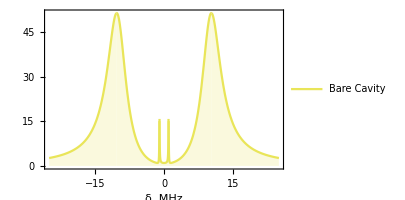

```mathematica
Clear[params, NormTrans]
params={{Γ->6,ΓR->.03, κ->4, g-> 20, ΩR-> 2, Ω-> .01, δac->0, ΔblueR->0, Δmwbox->0, ΓR2-> .03, gmm->2, κbox->.1}, {Γ->6,ΓR->.03, κ->4, g->  20, ΩR-> 2,Ω-> .01, δac->0, ΔblueR->0, Δmwbox->0, ΓR2-> .03, gmm->2, κbox->.1},{Γ->6,ΓR->.03, κ->4, g->  20, ΩR-> 2,Ω-> .01, δac->0, ΔblueR->0,Δmwbox->0, ΓR2-> .03, gmm->2, κbox->.1}};
NormTrans =(Abs[Trans/.params[[1]]]^2)/.δlc->0;
TransFinal =(((Abs[Trans])^2)/.params)/NormTrans;
Normg2 =((Abs[g2/.params])^2/ TransFinal^2)/.δlc-> 100;
g2Final =((Abs[g2/.params])^2 / TransFinal^2)/Normg2;
manyatomVRS =Plot[{TransFinal[[1]]}, {δlc, -25, 25}, PlotRange->All, PlotStyle->colorGradToIndexed["BlueGreenYellow", 1],Filling->Axis, PlotLegends-> Placed[{ "Bare Cavity", "VRS, 1 atom",  "VRS, 1000 atoms"}, Right],AspectRatio->2/3, ImageSize->300,ImagePadding->All,ImageMargins->0,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
```

# non-Hermitian Perturbation for mmwaves 2 excitations

```mathematica
ar=.25;fsize=18;
GenerateLabels[ts_]:=Table[{ts[[jj]],Style[ToString[ts[[jj]]],fsize-2]},{jj,1,Length[ts]}];
(*Generate allowed states*)
GetList[numphots_,maxpersite_]:=If[maxpersite=={},{{}},
Flatten[Table[
Table[Prepend[#[[kk]],jj],{kk,1,Length[#]}]&[GetList[numphots-jj,Rest[maxpersite]]],
{jj,0,Min[numphots,First[maxpersite]]}
],1]
]
```

```mathematica
OneVect[j_,nn_]:=Table[If[i==j,1,0],{i,1,nn}]
(*Define raising operators more systematically!
Define onsite and tunneling for site 0 (which is coupled only to site 1
Add one more photon max, and see what comes out!*)
```

```mathematica
nSites=5;(*Optical Cavity, E state, R state, Rp state, μcavity*)
nPhots=2;

States=GetList[nPhots,Table[nPhots,{nSites}]]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,2},{0,0,0,1,0},{0,0,0,1,1},{0,0,0,2,0},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,2,0,0},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,1,0,0},{0,2,0,0,0},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,1,0,0},{1,1,0,0,0},{2,0,0,0,0}}

```mathematica
VacState=OneVect[Position[States,ConstantArray[0,Length[States[[1]]]]][[1,1]],Length[States]]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Generate Raising and Lowering Operators*)
nS=Length[States]
aDs=Table[0*IdentityMatrix[nS],{jj,1,nSites}];
```

21

```mathematica
For[cS=1,cS≤nS, cS++,
curState=States[[cS]];
iSs=Table[Position[States,curState+OneVect[j,nSites]],{j,1,nSites}];
For[kk=1,kk≤nSites,kk++,
If[iSs[[kk]]≠{},aDs[[kk,iSs[[kk,1,1]],cS]]=√(curState[[kk]]+1.)];
]
]
```

```mathematica
as=Table[Transpose[aDs[[j]]],{j,1,nSites}];
```

```mathematica
ψo=as[[1]];ψoD=Transpose[ψo];
ψe=as[[2]];ψeD=Transpose[ψe];
ψr=as[[3]];ψrD=Transpose[ψr];
ψf=as[[4]];ψfD=Transpose[ψf];
ψμ=as[[5]];ψμD=Transpose[ψμ];

H0=δprobe(ψoD.ψo+ψeD.ψe+ψrD.ψr+ψfD.ψf+ψμD.ψμ)+g(ψeD.ψo+ψoD.ψe)+Ω(ψrD.ψe+ψeD.ψr)+gμ(ψμD.ψfD.ψr+ψrD.ψμ.ψf)+(δo+I κo/2)ψoD.ψo+(δe+I Γ/2)ψeD.ψe+(δr+I γr/2)ψrD.ψr+(δf+I γf/2)ψfD.ψf+(δμ+I κμ/2)ψμD.ψμ;
```

```mathematica
TCalc[parms_,retψ_:False]:=Module[{Hval,theparms,lldrive,zdrive,ψDriveD,Vval,ψ0,ψ1,ψ2,ψ2c,ψtC,ψDispD},
Hval=H0//.parms;
ψDriveD=ψoD;
Vval=(Ωprobe ψDriveD)//.parms;
ψ0=VacState;
ψ1=LinearSolve[Hval,Vval.ψ0];
ψ2=Chop[LinearSolve[Hval,Vval.ψ1]];
(*wavefunction projected into the two-photon sector, and normalized*)

retval={δprobe//.parms,Chop[Conjugate[ψ1].ψoD.ψo.ψ1],Chop[Conjugate[ψ2].ψoD.ψoD.ψo.ψo.ψ2]};
If[retψ==True,retval=Join[retval,{ψ1,ψ2}]];
retval
];
(*Inverse[Hval+IdentityMatrix[Length[Hval]] 10^-10.]*)
```

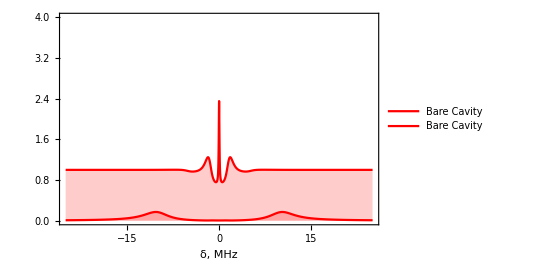

```mathematica
parms=
(* {Ωprobe->.1*2 π,δprobe->xx,g->10.*2 π,Ω->2.*2 π,gμ->2 π,δo->0.,κo->5*2 π,δe->0.
,Γ->6*2*π, δr->0,γr->.1*2*π,δf->0.,γf->0,δμ->0.,κμ->0.1*2 π};*)
{Ωprobe->.1,δprobe->xx,g->10,Ω->1.,gμ->2,δo->0.,κo->4.,δe->0.,Γ->6., δr->0,γr->.1,δf->0.,γf->.1,δμ->0.,κμ->5};
thedata=ParallelTable[TCalc[parms,False],{xx,-25,25,.01}];
Show[ListPlot[{#[[1]],(1/2#[[3]])/(1/2(#[[2]])^2)}&/@thedata,PlotRange->{0,4},Joined->True,Frame->True,PlotStyle->Red,FrameStyle->Directive[Black,14],PlotStyle->colorGradToIndexed["BlueGreenYellow", 1],Filling->Axis, PlotLegends-> Placed[{ "Bare Cavity", "VRS, 1 atom",  "VRS, 1000 atoms"}, Right],AspectRatio->2/3,ImageSize->400,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold},FrameStyle->Directive[Black,16]],ListPlot[{#[[1]],#[[2]]/(Ωprobe^2/(κo/2)^2)//.parms}&/@thedata,PlotRange->{0,1},Joined->True,PlotStyle->Red,FrameStyle->Directive[Black,14],PlotStyle->colorGradToIndexed["BlueGreenYellow", 1],Filling->Axis, PlotLegends-> Placed[{ "Bare Cavity", "VRS, 1 atom",  "VRS, 1000 atoms"}, Right],AspectRatio->2/3,ImageSize->400,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]]
```

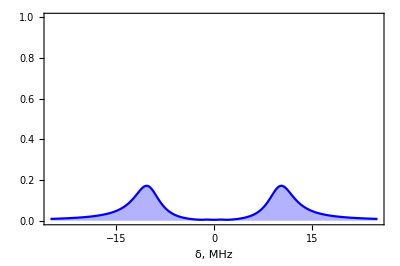

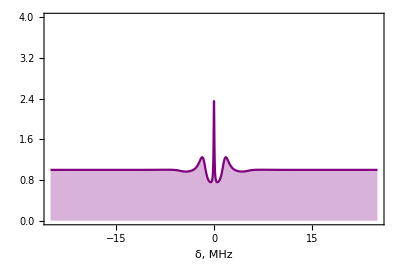

```mathematica
t1 =ListPlot[{#[[1]],#[[2]]/(Ωprobe^2/(κo/2)^2)//.parms}&/@thedata,PlotRange->{0,1},Joined->True,FrameStyle->Directive[Black,14],PlotStyle-> Blue,Filling->Axis,FillingStyle->Opacity[0.3],AspectRatio->2/3,ImageSize->400,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["Transmission", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold}]
g21 =ListPlot[{#[[1]],(1/2#[[3]])/(1/2(#[[2]])^2)}&/@thedata,PlotRange->{0,4},Joined->True,Frame->True,PlotStyle->Purple,FrameStyle->Directive[Black,14],PlotStyle->colorGradToIndexed["BlueGreenYellow", 1],Filling->Axis,FillingStyle->Opacity[0.3], AspectRatio->2/3,ImageSize->400,
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameLabel->{{ Style["", FontSize->12, Black],None},{Style["δ, MHz", FontSize->16, Black], Style["g_2 (0)", FontSize->16, Black, Bold]}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->16, Bold},FrameStyle->Directive[Black,16]]
```

```mathematica
Export["g21.pdf", g21]
```

g21.pdf

```mathematica
Export["t1.pdf", t1]
```

t1.pdf

# Rotating frame JCH 2nd excitation manifold

```mathematica
Clear[U, wl, t,δlc]
```

```mathematica
U =( {{1, 0, 0, 0, 0}, {0, Exp[ⅈ (wl ) t], 0, 0, 0}, {0, 0, Exp[ⅈ (wl ) t], 0, 0}, {0, 0, 0, Exp[ⅈ (2 wl ) t], 0}, {0, 0, 0, 0, Exp[ⅈ (2 wl ) t]}});
```

```mathematica
H = ( {{0, Ωo Exp[ⅈ (wl ) t], 0, 0, 0}, {Ωo Exp[-ⅈ (wl ) t], wc, 0, √2 Ωo Exp[ⅈ (wl ) t], 0}, {0, 0, wa, 0, 0}, {0, √2 Ωo Exp[-ⅈ (wl ) t], 0, 2 wc, 0}, {0, 0, 0, 0, wc + wa}});
```

```mathematica
Htr = FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0, t>0}])]//MatrixForm
```

(0 | Ωo | 0 | 0 | 0
Ωo | wc-wl | 0 | √2 Ωo | 0
0 | 0 | wa-wl | 0 | 0
0 | √2 Ωo | 0 | 2 (wc-wl) | 0
0 | 0 | 0 | 0 | wa+wc-2 wl)

```mathematica
FullSimplify[FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0, t>0}])] - IdentityMatrix[5]*(wc - wl)]//MatrixForm
```

(-wc+wl | Ωo | 0 | 0 | 0
Ωo | 0 | 0 | √2 Ωo | 0
0 | 0 | wa-wc | 0 | 0
0 | √2 Ωo | 0 | wc-wl | 0
0 | 0 | 0 | 0 | wa-wl)

# Rotating frame JCH 2nd excitation manifold collective

```mathematica
Clear[U, wl, t,δlc]
```

```mathematica
U =( {{1, 0, 0, 0, 0}, {0, Exp[ⅈ (wl ) t], 0, 0, 0}, {0, 0, Exp[ⅈ (wl ) t], 0, 0}, {0, 0, 0, Exp[ⅈ (2wl ) t], 0}, {0, 0, 0, 0, Exp[ⅈ (2wl ) t]}});
```

```mathematica
H = ( {{0, Ωo Exp[ⅈ (wl ) t], 0, 0, 0}, {Ωo Exp[-ⅈ (wl ) t], wc, 0, √2 Ωo Exp[ⅈ (wl ) t], 0}, {0, 0, wa, 0, 0}, {0, √2 Ωo Exp[-ⅈ (wl ) t], 0, 2 wc, 0}, {0, 0, 0, 0, wc + wa}});
```

```mathematica
Htr = FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0, t>0}])]//MatrixForm
```

(0 | Ωo | 0 | 0 | 0
Ωo | wc-wl | 0 | √2 Ωo | 0
0 | 0 | wa-wl | 0 | 0
0 | √2 Ωo | 0 | 2 (wc-wl) | 0
0 | 0 | 0 | 0 | wa+wc-2 wl)

```mathematica
FullSimplify[FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0, t>0}])] - IdentityMatrix[5]*(wc - wl)]//MatrixForm
```

(-wc+wl | Ωo | 0 | 0 | 0
Ωo | 0 | 0 | √2 Ωo | 0
0 | 0 | wa-wc | 0 | 0
0 | √2 Ωo | 0 | wc-wl | 0
0 | 0 | 0 | 0 | wa-wl)

# Rotating frame EIT

```mathematica
Clear[U, wl, t,δlc]
U =( {{1, 0, 0, 0}, {0, Exp[ⅈ (wl ) t], 0, 0}, {0, 0, Exp[ⅈ (wl ) t], 0}, {0, 0, 0, Exp[ⅈ (wb +wl ) t]}});

H = ( {{0, Ωo Exp[ⅈ (wl ) t], 0, 0}, {Ωo Exp[-ⅈ (wl ) t], wc, 0, 0}, {0, 0, wa, Ωr Exp[ⅈ (wb ) t]}, {0, 0, Ωr Exp[-ⅈ (wb) t], wr}});
Htr = FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0,wb>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0,wb>0, t>0}])]//MatrixForm
```

(0 | Ωo | 0 | 0
Ωo | wc-wl | 0 | 0
0 | 0 | wa-wl | Ωr
0 | 0 | Ωr | -wb-wl+wr)

```mathematica
FullSimplify[FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0,wb>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0,wb>0, t>0}])] - IdentityMatrix[4]*(wc - wl)]//MatrixForm
```

(-wc+wl | Ωo | 0 | 0
Ωo | 0 | 0 | 0
0 | 0 | wa-wc | Ωr
0 | 0 | Ωr | -wb-wc+wr)

# Rotating frame MM-wave

```mathematica
Clear[U, wl, t,δlc]
U =( {{1, 0, 0, 0}, {0, Exp[ⅈ (wl ) t], 0, 0}, {0, 0, Exp[ⅈ (wl ) t], 0}, {0, 0, 0, Exp[ⅈ (wb +wl ) t]}});

H = ( {{0, Ωo Exp[ⅈ (wl ) t], 0, 0}, {Ωo Exp[-ⅈ (wl ) t], wc, 0, 0}, {0, 0, wa, Ωr Exp[ⅈ (wb ) t]}, {0, 0, Ωr Exp[-ⅈ (wb) t], wr}});
Htr = FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0,wb>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0,wb>0, t>0}])]//MatrixForm
```

(0 | Ωo | 0 | 0
Ωo | wc-wl | 0 | 0
0 | 0 | wa-wl | Ωr
0 | 0 | Ωr | -wb-wl+wr)

```mathematica
FullSimplify[FullSimplify[(ⅈ D[U, t].FullSimplify[ConjugateTranspose[U],  Assumptions->{  wc>0,wl>0,wb>0, t>0}]+ U.H.FullSimplify[ConjugateTranspose[U],  Assumptions->{ wc>0, wl>0,wb>0, t>0}])] - IdentityMatrix[4]*(wc - wl)]//MatrixForm
```

(-wc+wl | Ωo | 0 | 0
Ωo | 0 | 0 | 0
0 | 0 | wa-wc | Ωr
0 | 0 | Ωr | -wb-wc+wr)

# Coupling strength

```mathematica
Clear[dn, a0]
a0 = 1/α ℏ/(me c);
e = 1.60217662×10^-19;
ℏ = 6.62607004×10^-34;
c = 3*10^8;
me = 9.10938356×10^-31;
α = .;
α1 = 1/137;
Ry = α^2/2 me c;
μn[n_] := (e a0 n^2)/(√2);
Γn[n_]:= 4/3 Ry/ℏ α^3 n^-5 ;
rn[n_]:= a0 n^2;
ωn [n_]:= (ℏ n)/(me rn[n]^2);
gn [n_]:= (2 c^2 me)/(π ℏ)α^(7/2)/n^4;
```

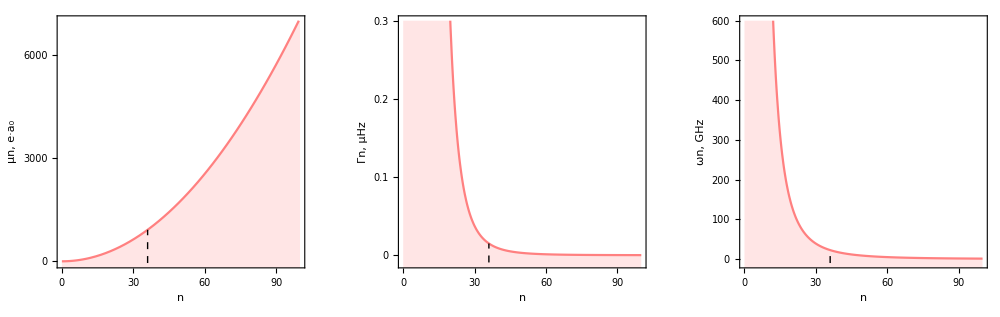

```mathematica
lineStyle={Thick,Black,Dashed};
line1=Line[{{36,-50},{36,(μn[36]/(a0*e))/.α->α1}}];
line2=Line[{{36,-.3},{36,Γn[36]/(2Pi 10^-6)/.α->α1}}];
line3=Line[{{36,-10},{36,ωn[36]/(2Pi 10^9)/.α->α1}}];
RydbergPlots =GraphicsRow[{Plot[(μn[n]/(a0*e))/.α->α1, {n, 0, 100},PlotRange-> {-50, 7000}, PlotStyle->Pink,AspectRatio->1,Filling-> -1000.1 ,FrameLabel->{{Style["μn, e·a_0", FontSize->18, Black], None},{Style["n", FontSize->18, Black],None}},
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameTicks->{{{0, 3000, 6000}, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->18, Bold},Epilog->{Directive[lineStyle],line1}],Plot[Γn[n]/(2Pi 10^-6)/.α->α1, {n, 0, 100},PlotStyle->Pink,AspectRatio->1 ,PlotRange-> {-.01,.3}, Filling -> -0.3,FrameLabel->{{Style["Γn, μHz", FontSize->18, Black], None},{Style["n", FontSize->18, Black],None}},
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameTicks->{{{0,0.1, 0.2, 0.3}, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->18, Bold},Epilog->{Directive[lineStyle],line2}],Plot[ωn[n]/(2Pi 10^9)/.α->α1, {n, 0, 100},PlotStyle->Pink,AspectRatio->1 ,PlotRange-> {-10,600}, Filling -> -1000.1,FrameLabel->{{Style["ωn, GHz", FontSize->18, Black], None},{Style["n", FontSize->18, Black],None}},
Frame-> {{True, True},{True, True}}, FrameStyle-> {{Black, Automatic},{Black, Automatic}},FrameTicks->{{Automatic, None},{Automatic, None}},FrameTicksStyle->Directive[ Black],BaseStyle->{FontWeight->Automatic,FontSize->18, Bold},Epilog->{Directive[lineStyle],line3}]},ImageSize->1000]
```

```mathematica
Export["RydbergPlots.pdf",RydbergPlots]
```

RydbergPlots.pdf

```mathematica
Γn[n]
```

(2.74956×10^11 α^5)/n^5

```mathematica
ωn[n]
```

(1.2373×10^20 α^2)/n^3

```mathematica
gn[n]/.α->α1
```

(2.61718×10^12)/n^4

```mathematica
gn[n]
```

(7.8769×10^19 α^(7/2))/n^4

```mathematica
(1/137.)^(7/2)
```

3.3226×10^-8

```mathematica
κ = 1 10^6;
Γ =6 10^6;
```

```mathematica
(gn[5]/.α->α1)^2
```

1.75351×10^19

```mathematica
(gn[35]/.α->α1)^2/(κ*Γ)
```

0.506958

```mathematica
((gn[36]/.α->α1)^2/(κ*Γ))
```

252916.

```mathematica
gn[6]/.α->α1
```

2.01943×10^9

```mathematica
gt[n_]:=(c me^(1/2))/π α n^(-3/2)
```

```mathematica
gt[36]/.α->α1
```

3.07994×10^-12

```mathematica
(c me^(1/2))/π
```

9.11414×10^-8